# Advanced Mathematics Assignment

Marcio Reverbel - VUB Student #: 0574770

## 1. Global Immunization Coverage

“In a devastating example of critical thinking gone bad, highly educated, deeply caring parents avoid the vaccinations that would protect their children from killer diseases. I love critical thinking and I admire skepticism, but only within a framework that respects evidence. So if you are skeptical about the measles vaccination, I ask you to do two things. First, make sure you know what it looks like when a child dies from measles. Most children who catch measles recover, but there is still no cure and even with the best modern medicine, one or two in every thousand will die of it. Second, ask yourself, “What kind of evidence would convince me to change my mind?” If the answer is “no evidence could ever change my mind about vaccination,” then you are putting yourself outside evidence-based rationality, outside the very critical thinking that first brought you to this point. In that case, to be consistent in your skepticism about science, next time you have an operation please ask your surgeon not to bother washing her hands.”

Rosling, H., Rosling, O., & Rönnlund, A. R. (2018). Factfulness: Ten reasons we’re wrong about the world – and why things are better than you think. Sceptre.

This dataset contains time series data on the coverage of several different vaccines, organized per country. Next I will perform some basic exploratory data analysis, verifying how many countries are represented and which vaccines are included in the data. I also look more closely at the MCV1 vaccine against measles, and map the different levels of coverage against measles around the globe in 2018. Then I created a Time Series Diagram of the measles coverage in the UK (where the modern anti-vax movement was born). Finally, I finish with a group of Time Series diagrams showing the coverage of 5 different vaccines (the ones for which we have most data) on 5 different countries (arbitrarily chosen).

## 1.1 Data set

```mathematica
ResourceObject["Global Immunization Coverage"];
data = ResourceData[ResourceObject["Global Immunization Coverage"]];
```

```mathematica
CountryList = DeleteDuplicates[data[All,1]]; (* I select the first column of the set and delete all duplicated information to create list of countries included in the data set. *)
```

```mathematica
Dimensions[CountryList] (* The Dimension, in this context, tells us how many countries there are. *)
```

{194}

194 countries are included in this dataset.

```mathematica
VaccineList = DeleteDuplicates[data[All, 2]]
```

```mathematica
Dimensions[VaccineList]
```

{46}

The dataset includes information on the coverage for 46 different vaccines. 

Then I use Tally to see for which vaccines we have the biggest amount of data. When sorting, "Last" refers to the last element in the expression: the number of counts. ("First" would sort based on the names of the vaccines.)

```mathematica
ReverseSortBy[Last][Tally[Values[data[All, 2;;2]]]]
```

## 1.2 Creating different coverage groups

Next I manipulate the data to see what the coverage for a specific vaccine looks like on a world map for the most recent year in the data set (2018). I Select the part of the data consistent with that year and with the chosen vaccine, MCV1 (measles-containing vaccine - 1st dose). Countries are presented from highest to lowest coverage.

```mathematica
newdata = data[Select[And[
#vaccine=="MCV1",
#year==DateObject[{2018}]
]&]/*ReverseSortBy[#coverage&]]                                                 (* I made use of the RightComposition for functions to make code visualisation more clear => f/*g == g[f] *)
```

Here, I clean the new data by removing the vaccine and year columns (redundant information) and I sort the coverage from lowest to highest instead.

```mathematica
SortByCoverage = newdata[SortBy[#coverage&], {"country", "coverage"}]
```

I separated the new data into different groups based on each country's level of coverage.

```mathematica
Immunity1 = SortByCoverage[Select[#coverage > 0.95&]]
```

```mathematica
Immunity2 = SortByCoverage[Select[#coverage <= 0.95&& #coverage > 0.9&]]
```

```mathematica
Immunity3 = SortByCoverage[Select[#coverage <= 0.9&& #coverage > 0.8&]]
```

```mathematica
Immunity4 = SortByCoverage[Select[#coverage <= 0.8&& #coverage > 0.7&]]
```

```mathematica
Immunity5= SortByCoverage[Select[#coverage <= 0.7&]]
```

## 1.3 A map of the 5 coverage groups

Finally, I create a visualization of the data on a map. Each group of countries is attributed its own color, and a legend provides information on the coverage-level for each group.

```mathematica
CoverageMap = GeoListPlot[{Immunity1, Immunity2, Immunity3, Immunity4, Immunity5}, 
PlotLegends -> {"]95%, 100%]", "]90%, 95%]", "]80%, 90%]", "]70%, 80%]","[0%, 70%]" }, 
PlotLabel->"Measles Vaccine Coverage",
GeoLabels -> False]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./resources/coverage_map.png", CoverageMap];
```

/home/mreverbel/Studies/VUB - Bachelors/Semester 3/Advanced Mathematics/Wolfram Mathematica/project

./resources/coverage_map.png

## 1.4 UK Time-Series

Next, I look at the data in a longitudinal way. Now I select one country (UK) and one vaccine (MCV1). The Entity object is used to make use of Wolfram's pre-defined "Country" Entity (which among other things, presents country's names in a nicer format. More importantly, it gives access to a series of data pre-organized per country, but this feature is not used here).

```mathematica
data[Select[And[
#vaccine=="MCV1",
#country==Entity["Country", "UnitedKingdom"]
]&]]
```

The function below selects part of the data, based on the country and on the vaccine, and returns a TimeSeries-type. The most important thing to notice is the SetDelayed[lhs, rhs] or "lhs := rhs", which assigns rhs to the symbol lhs without having first evaluated rhs. rhs is then evaluated whenever lhs would be evaluated later in the code. This allows me reevaluate VaccineTimeSeries with new data each time it is called, meaning that I can iterate through different countries and vaccines to create different TimeSeries without needing to write too much code. (More details on the notation are explored in the Appendix.)

DateListPlot creates the visualization. GridLines was used to create a horizontal dashed line at the 90% coverage, a vertical red line highlighting when the fraudulent paper that launched the modern "anti-vax" movement was published (February, 1998, by Andrew Wakefield), and another vertical green line highlighting Brian Deer's investigative report (the first of many) on the Sunday Times which exposed the fraud.

UnitedKingdom

MCV1

TimeSeries[…]

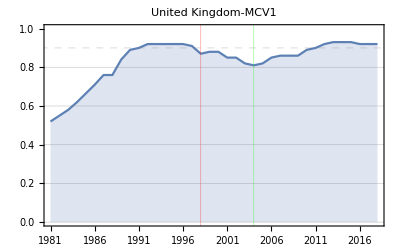

```mathematica
VaccineTimeSeries[country_Entity,vaccine_String]:=
data[Select[And[
#country===country,
#vaccine===vaccine
]&]][TimeSeries[Values/@#]&,{"year","coverage"}] (* Further explained in the Appendix *)

c = "UnitedKingdom"
v = "MCV1"

VaccineTimeSeries[Entity["Country",c],v]

ts = DateListPlot[VaccineTimeSeries[Entity["Country",c],v],
Filling-> Axis,
GridLines-> {{{"1998", Red}, {"2004", Green}},{0.0, 0.2,0.4,0.6, 0.8, {0.9, Dashed}}},
PlotRangePadding->None,
PlotRange->{0,1},
PlotLabel ->  Text[Entity["Country", c] - v]]
```

```mathematica
Export["./resources/UK_timeseries.png", ts];
```

./resources/UK_timeseries.png

## 1.5 A 5x5 matrix of time-series diagrams

Now for some final exploratory data analysis: The purpose is to create Time Series diagrams for the immunizations for which there are more data, and for 5 arbitrarily chosen countries (4 countries where I've lived plus my wife's country of birth). 

First, I discovered which vaccines have the most amount of data:

```mathematica
ReverseSortBy[Last][Tally[Values[data[All, 2;;2]]]][1;;5,1] (* "Last" gets the last value of the association created by the Tally => So the ReverseSort is based on the counts. [1;;5,1] selects the first five rows and the first column of the reverse sorted Tally. *)
```

The following line of code uses the same call for the VaccineTimeSeries function used in the UK example above as input to a Table creating a 5x5 matrix of time series plots, in which each row of the matrix is determined by the immunization type, and each column by the country represented. The SetDelayed (:=) of the VaccineTimeSeries allows me to avoid writing too much code, since values are only evaluated when VaccineTimeSeries is called, and each time it is called with a different set of values (via iteration under Table). The MatrixForm helps to maintain a stable 5x5 visual format, regardless of the computer display of who is viewing the data.

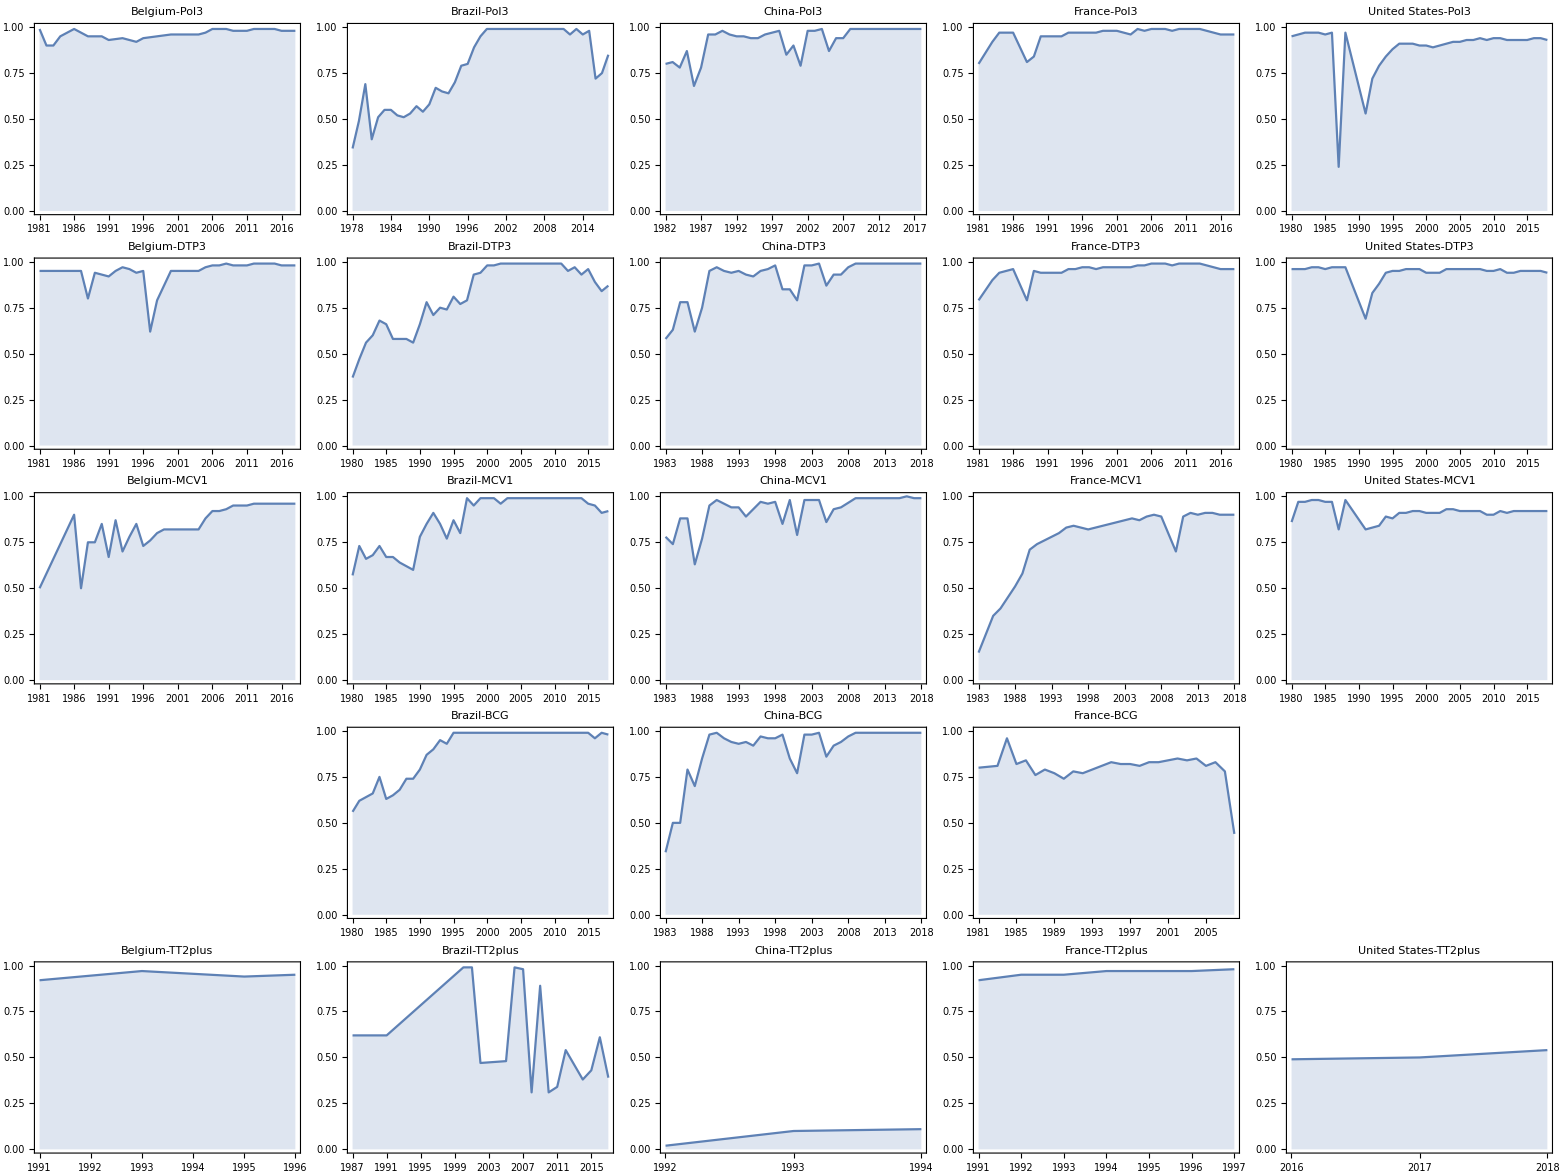
(-Graphics-)

./resources/matrix.png

```mathematica
TSmatrix = MatrixForm[
Table[
DateListPlot[VaccineTimeSeries[Entity["Country",c],v],
Filling-> Axis,
GridLines-> Automatic,
PlotRangePadding->None,
PlotRange->{0,1},
PlotLabel ->  Text[Entity["Country", c] - v]], 
{v, {"Pol3", "DTP3", "MCV1", "BCG", "TT2plus"}},
{c, {"Belgium", "Brazil", "China","France", "UnitedStates"}}
]
]

Export["./resources/matrix.png", TSmatrix];
(* Pol3 is a vaccine against Polio, DTP3 is a trivalent vaccine for diphteria, tetanus and pertussis, MCV1 is for measles, BCG is for tuberculosis, and TT2plus is for tetanus. Some countries don't have data for the BCG vaccine. *)
```

## 2. Global Mean Temperatures

"When you have an established scientific emergent truth, it is true whether or not you believe in it, and the sooner you understand that, the faster we can get on with the political conversations about how to solve the problems that face us. So once you understand that humans are warming the planet, you can then have a political conversation about that ." 
Neil deGrasse Tyson

https://www.youtube.com/watch?v=8MqTOEospfo

This dataset contains measurements of the average global temperature in relation to a base period (1951-1980) and in various forms (Monthly, Yearly, and in seasonal periods). Next I will calculate some approximations to compare the data to itself, verify what the base period actually represents, and create a Time Series diagram exposing the very clear increase in the Earth's average temperature.

## 2.1 Data set

```mathematica
ResourceObject["NASA GISTEMP Global Means dTs"]
data2 = ResourceData[ResourceObject["NASA GISTEMP Global Means dTs"]]
```

ResourceObject[…]

The first thing I chose to do is to compare the data pertaining to the whole yearly average (JanToDec) with a manually calculated average of the monthly data, to see how good the latter approximates the former. Some difference is expected, since the unequal length of different months should result in a slightly different weight of some data in relation to others, and which are simplified when the arithmetic mean is used. Nonetheless, it is an interesting exercise, and the differences should be very small. 

First, I selected only the monthly data. I also cut out the last row (year 2016), since it's data is incomplete:

```mathematica
Monthly = data2[1;;136, 1;;13]
```

Then, I calculated the yearly mean by making the arithmetic average of the temperatures of the twelve months for each year:

```mathematica
CalculatedYearlyMean =Map[Mean, Monthly[All, 2;;13]]  (*I Map the Mean function onto each row of the Monthly matrix.*)
```

A small difference can indeed be noticed below (although it could be due to rounding issues). The arithmetic mean of the average temperature of the twelve months serves, nonetheless, as a pretty decent approximation for the yearly average temperature.

```mathematica
For[i = 1, i <= 10, i++, Print[{data2[i, 14], CalculatedYearlyMean[i]}]]
Print["..."]
```

{-0.2 °C,-0.2 °C}

{-0.11 °C,-0.110833 °C}

{-0.09 °C,-0.0925 °C}

{-0.19 °C,-0.193333 °C}

{-0.27 °C,-0.269167 °C}

{-0.3 °C,-0.3 °C}

{-0.29 °C,-0.294167 °C}

{-0.32 °C,-0.321667 °C}

{-0.2 °C,-0.1975 °C}

{-0.11 °C,-0.106667 °C}

...

Next, it is possible to determine what are the highest and lowest average yearly temperatures registered (using JanToDec) and the difference between the two extremes. The Apply function, in combination with Subtract, is used on the output of the MinMax function to calculate the difference between the two values.

```mathematica
deltaMax = MinMax[data2[1;;136,14]]
Apply[Subtract, Reverse[deltaMax]] (* Reverse is used to calculate T2 - T1, instead of T1 - T2. *)
```

{-0.47 °C,0.86 °C}

1.33 °C

Another interesting thing to note refers to the meaning of the temperatures. They are temperature differences in relation with a base period spanning 30 years from 1951 to 1980. This means that the average relative temperature from this base period should be set at 0, from which the difference in temperature of other years in relation to this period can be seen. 

I've calculated this mean below (which is very close to 0, as expected -> 0.000333333), by Selecting the relevant period and using the Mean function:

```mathematica
BasePeriod = data2[Select[#Year > DateObject[{1950}] && #Year <= DateObject[{1980}]&]][All, 14]
Mean[BasePeriod]
```

-0.000333333 °C

Next I found the years that correspond to the highest and lowest average temperatures measured (always in relation with the base period). The For loop is used to iterate through the rows of the dataset and look for the two temperatures (found earlier by the MinMax function and stored in deltaMax) in the 14th column (JanToDec):

```mathematica
For[i = 1, i < 137, i++, If [data2[i,14]== deltaMax[[1]]|| data2[i,14]== deltaMax[[2]], Print[data2[i, 1;;14;;13]]]]
Print["The biggest temperature difference between yearly global mean temperatures is"Text[Subtract@@Reverse[deltaMax]]]
```

The biggest temperature difference between yearly global mean temperatures is 1.33 °C

## 2.2 Time Series Diagram of the Global Mean Temperature

Finally, I finish this exploratory analysis with a Time Series Diagram, providing a visualization for the change in the Global Mean Temperature (using 1951-1980 as a base period) as measured by NASA's Goddard Institute for Space Studies. 

The YearlyTemperatureTimeSeries data is formulated in a similar manner as the VaccineTimeSeries was done in the previous chapter, except it is now much simpler, as I do not need to iterate through different values to create multiple plots. I start by creating a TimeSeries-type data based on the year (Year) and average yearly temperatures (JanToDec). Then the DateListPlot called with the YearlyTemperatureTimeSeries as input. 

The plot shows the base period in between the dashed lines, and the years with the highest and lowest temperatures are marked by vertical red lines. 

The graph shows a clear increase in temperature, which seems to have taken place at a higher rate from the 1970s onwards.

TimeSeries[…]

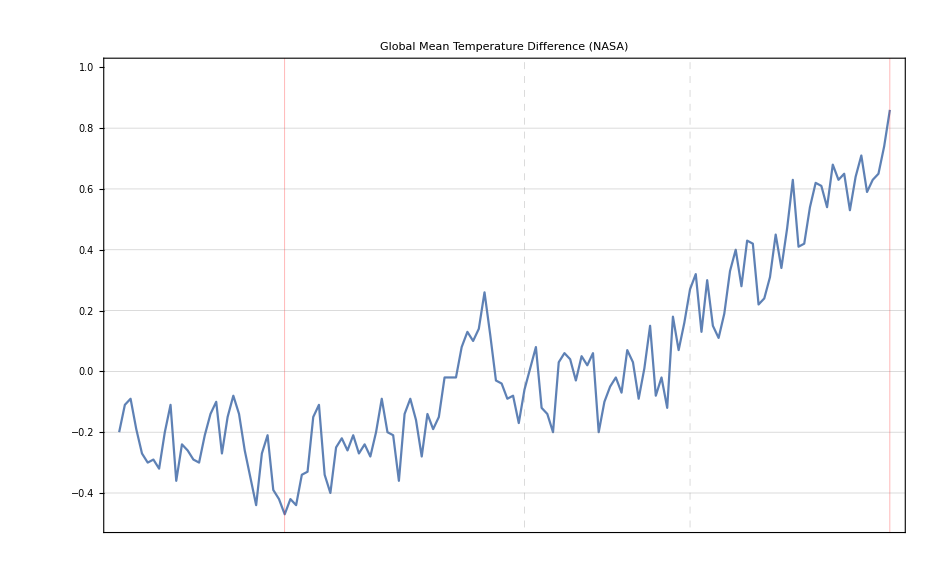

```mathematica
YearlyTemperatureTimeSeries =data2[TimeSeries[Values/@#]&,{"Year","JanToDec"}]

maxmintemp = DateListPlot[YearlyTemperatureTimeSeries, 
Filling-> None,
GridLines-> {{{"1909", Red}, {"1951", Dashed},{ "1980", Dashed},{"2015", Red}},{-0.4, -0.2, 0.0, 0.2,0.4,0.6, 0.8}},
PlotRangePadding-> True,
PlotRange->{-0.5, 1},
PlotLabel ->  Text["Global Mean Temperature Difference (NASA)"]]

Export["./resources/maxmin_temperature.png", maxmintemp];
```

## 3. Appendix

The following section is meant as an exploration into the differences in output when we change the input to the core of the VaccineTimeSeries function*. 

Observe what happens when changing from "All" to  "Values/@#&" (equivalent to "Map[Values, {#}]) &" to "TimeSeries[Values/@#&]":

*(for the purpose of this example, we don't use SetDelayed.)

```mathematica
Table[{
data[Select[And[
#country=== Entity["Country", "Brazil"], (* When applied to an association,#name is equivalent to #["name"] and picks out elements in the association. *)
#vaccine==="MCV1"
]&]][1;;2, All][All,{"year","coverage"}],

data[Select[And[
#country=== Entity["Country", "Brazil"],
#vaccine==="MCV1"
]&]][1;;2, All][Values/@#&,{"year","coverage"}], (* # (Slot1) represents the first argument supplied to a pure function => In this case, the keys of the Association. *)

data[Select[And[
#country=== Entity["Country", "Brazil"],
#vaccine==="MCV1"
]&]][1;;2, All][Map[Values,{#}]&,{"year","coverage"}],

data[Select[And[
#country=== Entity["Country", "Brazil"],
#vaccine==="MCV1"
]&]][1;;2, All][TimeSeries[Values/@#]&,{"year","coverage"}]},
1]
```

{{,,,TimeSeries[…]}}